```mathematica
StepResponse[t_,a_,μ1_,μ2_,τ_,b_]:=a(HeavisideTheta[t-μ1](1-Exp[-(t-μ1)/τ])-HeavisideTheta[t-μ2](1-Exp[-(t-μ2)/τ]))+b
```

```mathematica
MultiState[t_,n_,τ_,b_,a_List, μ_List]:=Module[{s},InverseLaplaceTransform[(∑_(i=1)^n a⟦i⟧/s Exp[-μ⟦i⟧s])1/(1+τ s),s,t]+b]
```

```mathematica
DigitizeFunction[f_,Fs_,tmax_]:=Block[{t},
Return[Table[N[{t,f[t]}],{t,0,tmax,10^6/Fs}]]
]
```

```mathematica
DigitizeFunction[f_,Fs_,tmax_,σ_]:=Block[{t},
Return[Table[N[{t,f[t]+RandomReal[NormalDistribution[0,σ]]}],{t,0,tmax,10^6/Fs}]]
]
```

### Event Processing Test Data

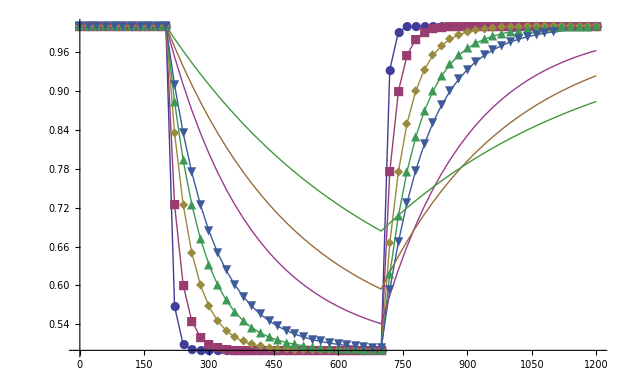

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,10^-9]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

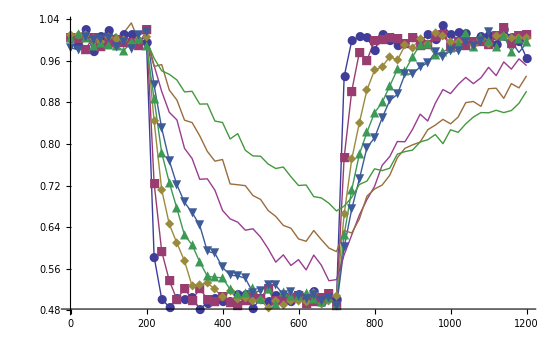

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,0.01]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

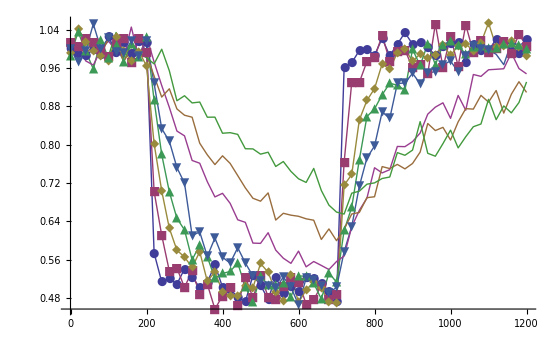

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,0.02]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

```mathematica
WriteTestEvent[datpath_,testname_,eventparams_List]:=Block[{
csvname=datpath<>testname<>".csv",
paramsname=datpath<>testname<>".prm",
eparams={"a","tau1","tau2","mu","b","Fs","tmax","noisepct"},
a=eventparams⟦1⟧,
τ1=eventparams⟦2⟧,
τ2=eventparams⟦3⟧,
μ=eventparams⟦4⟧,
b=eventparams⟦5⟧,
Fs=eventparams⟦6⟧,
tmax=eventparams⟦7⟧,
σ=eventparams⟦8⟧
},
Export[paramsname,ToString[#⟦1⟧]<>"="<>ToString[#⟦2⟧]&/@Transpose[{eparams,CForm/@eventparams}],"CSV"];
Export[csvname, DigitizeFunction[Evaluate[StepResponse[#,a,τ1,τ2,μ,b]&],Fs,tmax,σ],"CSV"];
]
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,10^-9}]&/@Transpose[{"test"<>ToString[#]&/@Range[1,8],{10,25,50,75,100,200,300,500}}];
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,0.01}]&/@Transpose[{"test"<>ToString[#]&/@Range[9,16],{10,25,50,75,100,200,300,500}}];
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,0.02}]&/@Transpose[{"test"<>ToString[#]&/@Range[17,24],{10,25,50,75,100,200,300,500}}];
```

### Multi-State Test Data

```mathematica
?MultiState
```

Global`MultiState

MultiState[t_,n_,a0_,τ_,b_,a_List,μ_List]:=Module[{s},InverseLaplaceTransform[a0/s+(∑_(i=1)^n (a⟦i⟧ Exp[-μ⟦i⟧ s])/s)/(1+τ s),s,t]+b]

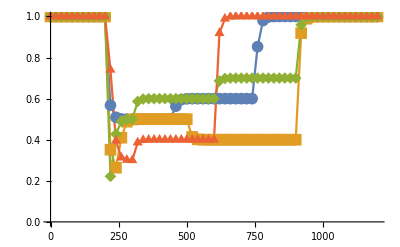

```mathematica
ListLinePlot[{
DigitizeFunction[Evaluate[MultiState[#,3,10,1,{-0.5,0.1,0.4},{200,450,750}]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[MultiState[#,4,10,1,{-0.75,0.25,-0.1,0.6},{200,250,500,900}]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[MultiState[#,5,10,1,{-0.9,0.4,0.1,0.1,0.3},{200,225,300,600,900}]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[MultiState[#,4,10,1,{-0.3,-0.4,0.1,0.6},{200,225,300,600,900}]&],50000,1200,10^-9]
},PlotRange->All,PlotMarkers->{Automatic,12},Joined->True]
```

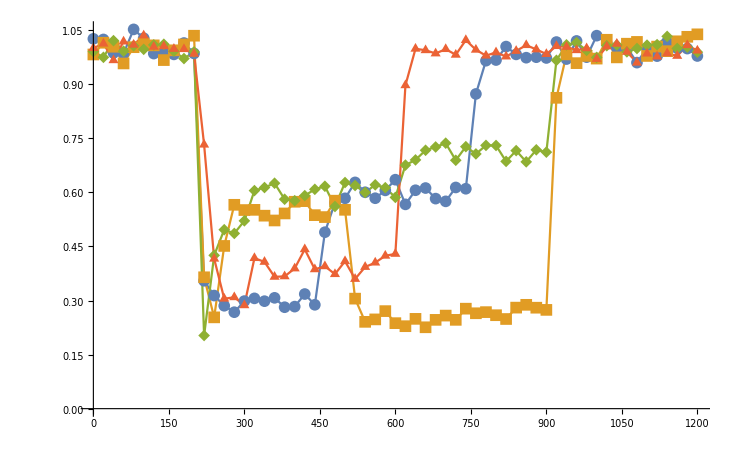

```mathematica
ListLinePlot[{
DigitizeFunction[Evaluate[MultiState[#,3,10,1,{-0.7,0.3,0.4},{200,450,750}]&],50000,1200,0.02],
DigitizeFunction[Evaluate[MultiState[#,4,10,1,{-0.75,0.3,-0.3,0.75},{200,250,500,900}]&],50000,1200,0.02],
DigitizeFunction[Evaluate[MultiState[#,5,10,1,{-0.9,0.4,0.1,0.1,0.3},{200,225,300,600,900}]&],50000,1200,0.02],
DigitizeFunction[Evaluate[MultiState[#,4,10,1,{-0.3,-0.4,0.1,0.6},{200,225,300,600,900}]&],50000,1200,0.02]
},PlotRange->All,PlotMarkers->{Automatic,12},Joined->True]
```

```mathematica
?MultiState
```

Global`MultiState

MultiState[t_,n_,τ_,b_,a_List,μ_List]:=Module[{s},InverseLaplaceTransform[(∑_(i=1)^n (a⟦i⟧ Exp[-μ⟦i⟧ s])/s)/(1+τ s),s,t]+b]

```mathematica
Clear[WriteTestEventMSA]
```

```mathematica
WriteTestEventMSA[datpath_,testname_,eventparams_List]:=Block[{
csvname=datpath<>testname<>".csv",
paramsname=datpath<>testname<>".prm",
eparams={"n","tau","tau1","tau2","b","a","mu","Fs","tmax","noisepct"},
n=eventparams⟦1⟧,
τ1=eventparams⟦5⟧⟦1⟧,
τ2=eventparams⟦5⟧⟦-1⟧,
τ=eventparams⟦2⟧,
b=eventparams⟦3⟧,
a=eventparams⟦4⟧,
μ=eventparams⟦5⟧,
Fs=eventparams⟦6⟧,
tmax=eventparams⟦7⟧,
σ=eventparams⟦8⟧
},
Export[paramsname,ToString[#⟦1⟧]<>"="<>ToString[#⟦2⟧]&/@Transpose[{eparams,CForm/@{n,τ,τ1,τ2,b,a,μ,Fs,tmax,σ}}],"CSV"];
Export[csvname, DigitizeFunction[Evaluate[MultiState[#,n,τ,b,a,μ]&],Fs,tmax,σ],"CSV"];
]
```

```mathematica
WriteTestEventMSA[NotebookDirectory[],"../testdata/msaTest1",{3,10,1,{-0.7,0.3,0.4},{200,450,750},50000,1200,10^-9}];
WriteTestEventMSA[NotebookDirectory[],"../testdata/msaTest2",{4,10,1,{-0.75,0.3,-0.3,0.75},{200,250,500,900},50000,1200,10^-9}];
WriteTestEventMSA[NotebookDirectory[],"../testdata/msaTest3",{5,10,1,{-0.9,0.4,0.1,0.1,0.3},{200,225,300,600,900},50000,1200,10^-9}];
```

### Event Partition Test Data

```mathematica
PEGEventTs[n_,τ_,b_,bσ_,Fs_]:=Module[{d,i},
d={ -RandomReal[UniformDistribution[{0.4,1}]],1100-RandomReal[NormalDistribution[0,25]],1600+RandomReal[NormalDistribution[0,25]]}&/@Range[n];

Return[Flatten[#⟦All,2⟧&/@Table[DigitizeFunction[Evaluate[StepResponse[#,d⟦i⟧⟦1⟧,d⟦i⟧⟦2⟧,d⟦i⟧⟦3⟧,τ,b]&],Fs,5000,bσ],{i,Range[Length[d]]}]]]
];
```

```mathematica
WriteTestEvent[datpath_,testname_,eventparams_List, testdatafunc_]:=Block[{
csvname=datpath<>testname<>".csv",
paramsname=datpath<>testname<>".prm",
eparams={"nevents","tau","i0","i0sig","Fs"}
},
Export[paramsname,ToString[#⟦1⟧]<>"="<>ToString[#⟦2⟧]&/@Transpose[{eparams,CForm/@eventparams}],"CSV"];
Export[csvname, testdatafunc@@eventparams,"CSV"];
]
```

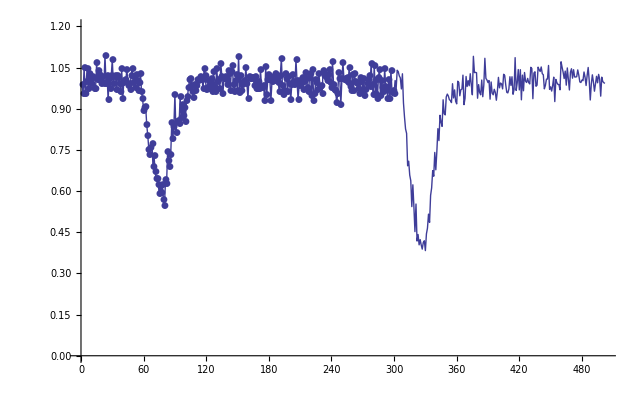

```mathematica
ListLinePlot[(PEGEventTs@@{2,200,1,0.033,50000}),PlotRange->{0,1.2},PlotMarkers->Automatic]
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/","testEventPartition"<>ToString[#⟦1⟧],{100,#⟦2⟧,1,0.033,50000},PEGEventTs]&/@Transpose[{Range[5],{10,50,100,150,200}}];//AbsoluteTiming
```

{4.85778,Null}